Temporal laser-pulse-shape effects in nonlinear Thomson scattering

V. Yu. Kharin, D. Seipt, and S. G. Rykovanov
PHYSICAL REVIEW A 93, 063801 (2016)

Notebook: Óscar Amaro, September 2022 @ GoLP-EPP

## Figure 2

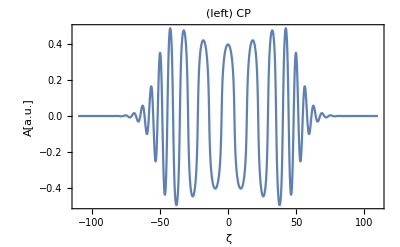

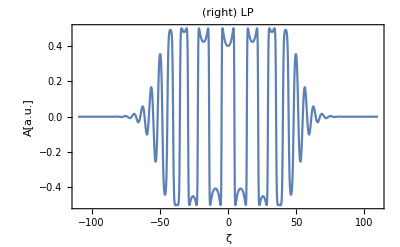

```mathematica
Clear[ζ,ξ,ALP,ACP,R,a,a0,τ,ϕ,int]
R=1;
a[ϕ_]:=a0 Exp[-ϕ^2/τ^2];
a0=2;
τ=20;
(* the integral has a full analytical solution *)
int=Integrate[(a0 Exp[-ξ^2/τ^2])^2 Cos[ξ]^2,{ξ,0,ϕ}];

(* eq 29 implicit relation, solve numerically*)
ϕ[ζ_]:=(FindRoot[ϕ+int-ζ,{ϕ,0}]//Quiet)[[1,2]]//Re//Quiet

(* eq 13 *)
ACP[ζ_]:=1/R a[ϕ[ζ]]/(1+a[ϕ[ζ]]^2)Cos[ϕ[ζ]]
(* eq 28 *)
ALP[ζ_]:=1/R(a[ϕ[ζ]]Cos[ϕ[ζ]])/(1+a[ϕ[ζ]]^2 Cos[ϕ[ζ]]^2)

(* lists *)
ACPlst = ParallelTable[{ζ,ACP[ζ]},{ζ,-110,+110,0.2}];
ALPlst = ParallelTable[{ζ,ALP[ζ]},{ζ,-110,+110,0.2}];

(* plots *)
ListPlot[ACPlst,Joined->True,Axes->False,Frame->True,FrameLabel->{"ζ","A[a.u.]"},PlotLabel->"(left) CP"]
ListPlot[ALPlst,Joined->True,Axes->False,Frame->True,FrameLabel->{"ζ","A[a.u.]"},PlotLabel->"(right) LP"]
```

## Table 1 / Figure 3 Gaussian

```mathematica
Clear[f,ϕ,a,τ,ω,d2I,χ,y,ff,fm1ξ,dfmi,a0]
f=Exp[-2x^2];
fm1=(Solve[f==ff,x][[2,1,2]]/.{C[1]->0})//Normal//Simplify;
fm1ξ = fm1/.{ff->ξ};
dfmi=D[fm1,ff];
y=(1-ω)/(a0^2 ω);
χ=Refine[ω τ a0^2 Integrate[fm1ξ,{ξ,y,1}]-π/4//Normal,{ω>0}];
d2I=(2ω τ)/π Abs[y dfmi/.{ff->y}]Cos[χ]^2;
d2I//Simplify
```

(τ ω Sin[1/4 (π+√2 τ (a0^2 √π ω Erf[√Log[-(a0^2 ω)/(-1+ω)]]+2 (-1+ω) √Log[-(a0^2 ω)/(-1+ω)]))]^2)/(√2 π √Abs[Log[-(a0^2 ω)/(-1+ω)]])

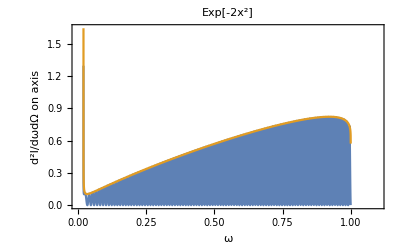

```mathematica
τ=10; (* choose 10 instead of 200 to see the oscillations, factor of 2 missing in table? *)
a0=7;
Plot[{(τ ω Sin[1/4 (π+√2 τ (a0^2 √π ω Erf[√Log[-(a0^2 ω)/(-1+ω)]]+2 (-1+ω) √Log[-(a0^2 ω)/(-1+ω)]))]^2)/(√2 π √Abs[Log[-(a0^2 ω)/(-1+ω)]]),2(ω τ)/(4π)(1/2 Log[(a0^2 ω)/(1-ω)])^-0.5},{ω,0,1.1},Frame->True,FrameLabel->{"ω","d^2I/dωdΩ on axis"},PlotLabel->"Exp[-2x^2]"]
```

## cos^2

```mathematica
Clear[f,ϕ,a,τ,ω,d2I,χ,y,ff,fm1ξ,dfmi,a0]
f=Cos[π x]^2;
fm1=(Solve[f==ff,x][[4,1,2]]/.{C[1]->0})//Normal//Simplify;
fm1ξ = fm1/.{ff->ξ};
dfmi=D[fm1,ff];
y=(1-ω)/(a0^2 ω);
χ=Refine[ω τ a0^2 Integrate[fm1ξ,{ξ,y,1}]-π/4//Normal,{ω>0}];
d2I=(2ω τ)/π Abs[y dfmi/.{ff->y}]Cos[χ]^2;
d2I//Simplify
```

(τ ω Abs[(1-ω)/(a0^2 ω √(-((-1+ω) (-1+ω+a0^2 ω))/(a0^4 ω^2)))] Sin[(π^2+2 a0^2 τ √(-((-1+ω) (-1+ω+a0^2 ω))/a0^4)+2 τ (-2+(2+a0^2) ω) ArcCos[(√((1-ω)/a0^2))/(√ω)])/(4 π)]^2)/π^2

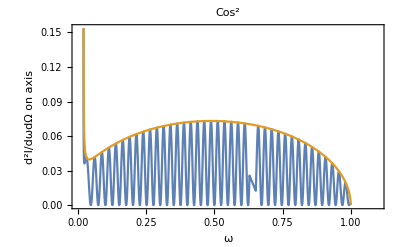

```mathematica
τ=10; 
a0=7;
Plot[{1/π^2 τ ω Abs[(1-ω)/(a0^2 ω √(-((-1+ω) (-1+ω+a0^2 ω))/(a0^4 ω^2)))] Sin[(π^2+2 a0^2 τ √(-((-1+ω) (-1+ω+a0^2 ω))/a0^4)+2 τ (-2+(2+a0^2) ω) ArcCos[(√((1-ω)/a0^2))/(√ω)])/(4 π)]^2,(ω τ)/π^2((a0^2 ω)/(1-ω)-1)^-0.5},{ω,0,1.1},Frame->True,FrameLabel->{"ω","d^2I/dωdΩ on axis"},PlotLabel->"Cos^2"]
```

## cos^4

```mathematica
Clear[f,ϕ,a,τ,ω,d2I,χ,y,ff,fm1ξ,dfmi,a0]
f=Cos[π x]^4;
fm1=(Solve[f==ff,x][[8,1,2]]/.{C[1]->0})//Normal//Simplify;
fm1ξ = fm1/.{ff->ξ};
dfmi=D[fm1,ff];
y=(1-ω)/(a0^2 ω);
χ=Refine[ω τ a0^2 Integrate[fm1ξ,{ξ,y,1}]-π/4//Normal,{ω>0}];
d2I=(2ω τ)/π Abs[y dfmi/.{ff->y}]Cos[χ]^2;
d2I//Simplify
```

(τ ω Abs[(((1-ω)/(a0^2 ω))^(1/4))/(√(1-√((1-ω)/(a0^2 ω))))] Sin[π/4+(τ (a0^2 √(1-(√((1-ω)/a0^2))/(√ω)) (2 √((1-ω)/a0^2)+3 √ω) ((1-ω)/a0^2)^(1/4) ω^(1/4)+(-8+(8+3 a0^2) ω) ArcCos[(((1-ω)/a0^2)^(1/4))/ω^(1/4)]))/(8 π)]^2)/(2 π^2)

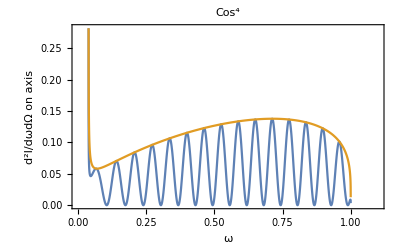

```mathematica
τ=10; 
a0=5;
Plot[{1/(2 π^2)τ ω Abs[(((1-ω)/(a0^2 ω))^(1/4))/(√(1-√((1-ω)/(a0^2 ω))))] Sin[π/4+1/(8 π)τ (a0^2 √(1-(√((1-ω)/a0^2))/(√ω)) (2 √((1-ω)/a0^2)+3 √ω) ((1-ω)/a0^2)^(1/4) ω^(1/4)+(-8+(8+3 a0^2) ω) ArcCos[(((1-ω)/a0^2)^(1/4))/ω^(1/4)])]^2,(ω τ)/(2π^2)(Sqrt[(a0^2 ω)/(1-ω)]-1)^-0.5},{ω,0,1.1},Frame->True,FrameLabel->{"ω","d^2I/dωdΩ on axis"},PlotLabel->"Cos^4"]
```

## Figure 4

Fig.4 left

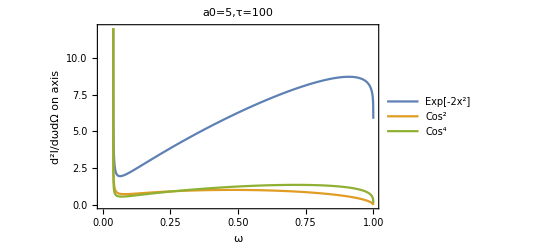

```mathematica
Clear[ω,τ,a0]
a0=5;
τ=100;
Plot[{2(ω τ)/(4π)(1/2 Log[(a0^2 ω)/(1-ω)])^-0.5,(ω τ)/π^2((a0^2 ω)/(1-ω)-1)^-0.5,(ω τ)/(2π^2)(Sqrt[(a0^2 ω)/(1-ω)]-1)^-0.5},{ω,0,1.1},Frame->True,FrameLabel->{"ω","d^2I/dωdΩ on axis"},PlotLabel->"a0=5,τ=100",PlotRange->{0,12},PlotLegends->{"Exp[-2x^2]","Cos^2","Cos^4"}]
```

Fig.4 right (a0=2 seems to match the figure, though one would have to normalize it with int |A|^2 fixed )

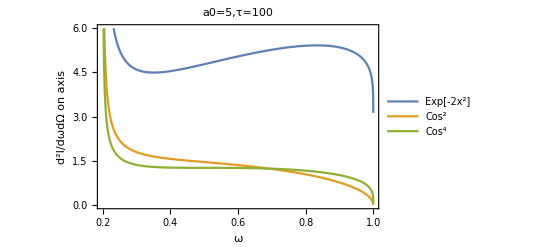

```mathematica
Clear[ω,τ,a0]
a0=2;
τ=50;
Plot[{2(ω τ)/(4π)(1/2 Log[(a0^2 ω)/(1-ω)])^-0.5,(ω τ)/π^2((a0^2 ω)/(1-ω)-1)^-0.5,(ω τ)/(2π^2)(Sqrt[(a0^2 ω)/(1-ω)]-1)^-0.5},{ω,0,1.1},Frame->True,FrameLabel->{"ω","d^2I/dωdΩ on axis"},PlotLabel->"a0=5,τ=100",PlotRange->{0,6},PlotLegends->{"Exp[-2x^2]","Cos^2","Cos^4"}]
```

## Jacobi-Anger expansion (example)

## Exp[-ϕ^4/100]

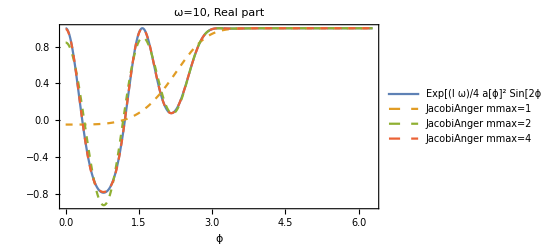

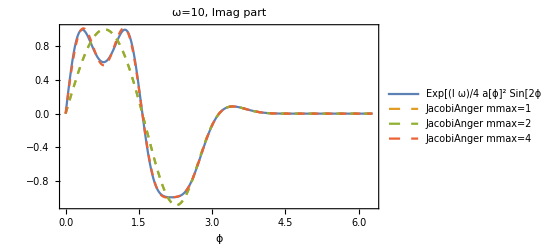

```mathematica
Clear[ϕ,a,ω,A2L,A2R,m,mmax]
a[ϕ_]:=Exp[-ϕ^4/100]
ω=10;
A2L[ϕ_]:=Exp[(I ω)/4 a[ϕ]^2 Sin[2ϕ]]
mmax=2;
A2R[ϕ_,mmax_]:=Sum[BesselJ[m,(ω a[ϕ]^2)/4]Exp[2I m ϕ],{m,-mmax,mmax}]

Plot[{Re[A2L[ϕ]],Re[A2R[ϕ,1]],Re[A2R[ϕ,2]],Re[A2R[ϕ,4]]},{ϕ,0,2π},PlotStyle->{Default,Dashed,Dashed,Dashed},Frame->True,FrameLabel->{"ϕ",""},PlotLegends->{"Exp[(I ω)/4 a[ϕ]^2 Sin[2ϕ]]","JacobiAnger mmax=1","JacobiAnger mmax=2","JacobiAnger mmax=4"},PlotLabel->"ω=10, Real part"]
Plot[{Im[A2L[ϕ]],Im[A2R[ϕ,1]],Im[A2R[ϕ,2]],Im[A2R[ϕ,4]]},{ϕ,0,2π},PlotStyle->{Default,Dashed,Dashed,Dashed},Frame->True,FrameLabel->{"ϕ",""},PlotLegends->{"Exp[(I ω)/4 a[ϕ]^2 Sin[2ϕ]]","JacobiAnger mmax=1","JacobiAnger mmax=2","JacobiAnger mmax=4"},PlotLabel->"ω=10, Imag part"]
```